# Projektövning - problemlösning i Mathematica

(Rapportskalet använder sig av ett stylesheet tillverkat av Göran Andersson)

Stefan Sarkis, Evan Saboo

## 1. Introduktion: problemformulering

Inom matematikkursen har vi fått i uppgift att lösa tre olika matematiska problem med hjälp av Mathematica och dess programmeringsspråk. Syftet med detta introduktionsprojekt är att öva matematisk modellering, Mathematica och rapportskrivning.

Dessa tre olika uppgifter handlar om att kunna skapa och modellera upp funktioner och hitta dess nollställen; modellera upp funktionens derivator och hitta dess nollställen; hitta skärningspunkter mellan två funktioner; skapa integraler och sist men inte minst kunna tolka graferna och dess resultat.

Målen med projektuppgifterna är att de ska underlätta inlärningen av kursinnehållet, de ska träna matematiskt modellbyggande samt att de ska ge träning i att tillverka och presentera rapporter.

### 1.1 Sammanfattning av uppgifter

I första deluppgiften var uppdraget att man först skulle modellera upp en tredjegradsfunktion och dess derivata. Funktionen som var tilldelad för denna uppgift är f(x)=x^3-ax^2+x+1 , där a är ett tal mellan 1 och 31. Man skulle även hitta nollställena för både tredjegradsfunktionen och derivatan. För att lösa första delen av uppgiften använde vi oss delvis av Plot[]-funktionen, vilket i Mathematica är den datatypen man använder för att modellera upp en funktion. I uppgiften skulle man bestämma de exakta lösningarna till funktionerna och använda sig av derivatas nollställen för att hitta maximumvärdet på intervallet. När vi lyckades räkna ut de exakta nollställena för funktionen för tredjegradsekvationen kunde vi med hjälp av nollställena modellera upp ett intervall för funktionen samt ta reda på funktionens maximumvärde i detta intervall.



Andra uppgiften gick ut på att man skulle modellera upp två funktioner och hitta skärningpunkten för dessa funktioner. Funktionerna man använde sig av är 2/(1+15 x^2) och 1/(√(1+15 x^2)). När man lyckades räkna ut skärningspunkten för funktionerna skulle man räkna ut integralen mellan dessa två funktioner. I Mathematica använder man sig av Integrate för att kunna räkna ut integraler av en eller flera funktioner.


Tredje uppgiften, även den sista för detta lilla projekt, skulle man första modellera två funktioner som repesenterar två generatorer. Den första funtkionen är y_1= A_1Sin(ωt + ϕ_1) och den andra funktionen är y_2= A_2Sin(ωt + ϕ_2). Den ena generator ger en spänning med amplitud A_1och fas ϕ_1, den andra ger en spänning med amplitud A_2 och fas ϕ_2. Båda har samma frekvens υ = 50 Hz.  ω står för vinkelfrekvensen, vilket är 2πυ. Vi ersatte amplituderna och faserna med olika värden för att kunna modellera funktonerna. När man lyckades få ut alla maximala punkter i funktionerna skulle man därefter modellera summan  av y_1 och y_2. Sedan skulle man undersöka  hur amplituden och fasen för summan verkar bero av amplituderna och faserna hos y_1 och  y_2. I den sista deluppgiften skulle man byta ut frekvensen till 60 Hz på en av funktionerna och modellera om summan de två funktionerna.

### 1.2 Sammanfattning del 2

## 2 Genomförande och härledningar

### 2.1 Uppgift 3.1)

För att modellera och rita ut tredjegradsfunktionen i första uppgiften och räkna ut dess nollställen använde vi oss datatypen Plot. Plot[]-funktionen används för att modellera upp funktionen inom ett intervall på -20 och 20 på x-axeln, med en “plotrange” på -1000 och 1000 som visas på y-axeln. I denna uppgift använde vi oss av ekvationen f(x)=x^3-ax^2+x+1  där vi valde att ha talet 15 som substitution för variabeln a. Vi börjar med att rensa alla globala variabler innan vi börjar modellera upp funktionen.

```mathematica
ClearAll["Global`*"]
```

```mathematica
?x
```

Global`x

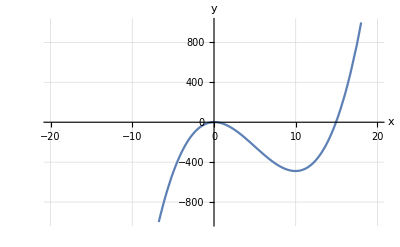

```mathematica
Plot[x^3-15 x^2+x+1, {x, -20, 20}, AxesLabel -> {"x","y"}, PlotRange ->{-1000, 1000}, LabelStyle->(FontSize->16), GridLines->Automatic]
```

Efter att vi modellerat upp grafen för tredjegradsfunktionen vill vi ta fram nollställen för funktionen. Detta görs med hjälp av en Epilog. Epilog används till för att sätta ut punkter på en graf, där vi då satte ut punkter på grafens nollställen, dvs. [x1, 0]; [x2, 0] och [x3, 0]. För att  räkna ut och få fram nollställena till funktionen gjorde vi följande:

```mathematica
f[x_]:=x^3-15x^2+x+1
```

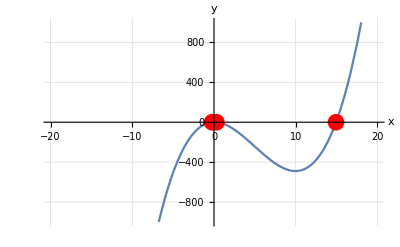

```mathematica
Plot[f[x], {x, -20, 20}, AxesLabel -> {"x","y"}, PlotRange->{-1000,1000}, LabelStyle->(FontSize->14), GridLines->Automatic, Epilog->{Red, PointSize[0.03], Point[{x1, 0}], Point[{x2, 0}], Point[{x3, 0}]}]
```

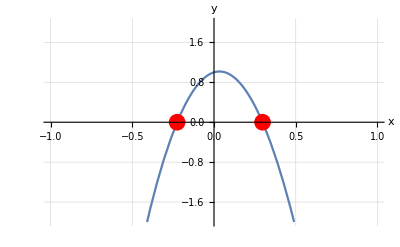

```mathematica
Plot[f[x], {x, -1, 1}, AxesLabel -> {"x","y"}, PlotRange->{-2, 2}, LabelStyle->(FontSize->14), GridLines->Automatic, Epilog->{Red, PointSize[0.03], Point[{x1, 0}], Point[{x2, 0}], Point[{x3, 0}]}]
```

Ovanför ser vi de två första nollställena mer noggrant på ett ekvationssystem inom intervallet [-1, 1]. Nedanför löser vi ut nollställena för tredjekradsfunktionen.

```mathematica
{x1,x2,x3}=x/.Solve[x^3-15 x^2+x+1 ==0,x];
x1
x2
x3
```

5+(2 (549+ⅈ √2517))^(1/3)/3^(2/3)+(37 2^(2/3))/(3 (549+ⅈ √2517))^(1/3)

5-((1+ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1-ⅈ √3))/(6 (549+ⅈ √2517))^(1/3)

5-((1-ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1+ⅈ √3))/(6 (549+ⅈ √2517))^(1/3)

Datatypen Solve används för att lösa ut alla exakta tal till nollställena för funktionen.

I nästa steg är uppgiften att ta fram derivatan av funktionen samt hitta dess nollställen. För att det göra allt lite mer förståeligt och snyggare löste vi ut nästa steg på följande sätt:

```mathematica
ClearAll["Global`*"]
?x
```

Global`x

```mathematica
f[x_]:= x^3-15 x^2+x+1
```

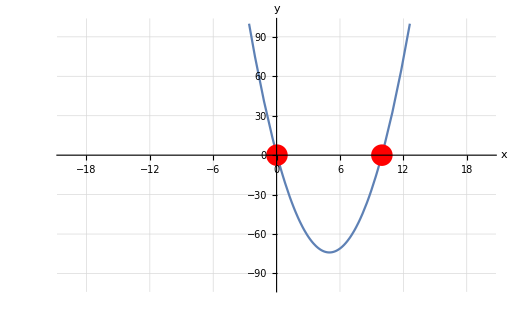

1/3 (15-√222)

1/3 (15+√222)

```mathematica
Plot[f'[x],{x,-20,20},AxesLabel->{"x","y"},PlotRange->{-100,100},LabelStyle->(FontSize->16),GridLines ->Automatic,Epilog->{Red,PointSize[0.03], Point[{x1,0}], Point[{x2,0}]}]

{x1,x2}=x/.Solve[f'[x]==0,x];
x1
x2
```

Ovan ser man att vi har gett f(x) den originalfunktion och sedan stoppat in det i Plot-funktionen. Istället för att räkna ut derivatan för hand och sedan skriva in det i Mathematica kan man låta programmet göra det åt en själv; då man plottat in f'(x), istället för att skriva in Plot[3x^-2 - 30x + , ...] på ett liknande sätt som gjordes för tredjegradsfunktionen.

Sista steget i denna uppgift var att modellera upp funktionen f(x) i ett intervall mellan de nollställen man fick fram, dvs [x_1,x_3], och därefter hitta maximum värdet i grafen. Vi löste uppgiften på detta sätt:

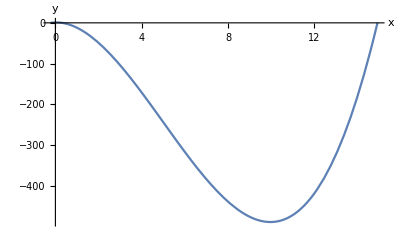

```mathematica
Plot[x^3-15 x^2+x+1,{x,5+(2 (549+ⅈ √2517))^(1/3)/3^(2/3)+(37 2^(2/3))/(3 (549+ⅈ √2517))^(1/3),5-((1-ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1+ⅈ √3))/(6 (549+ⅈ √2517))^(1/3)}, AxesLabel->{"x", "y"}]
```

```mathematica
x/.Last[FindMaximum[x^3-15 x^2+x+1,{x,1/3 (15-√222),1/3 (15+√222)}]]
```

0.0334452

Genom att använda Last[FindMaximum] kan vi hitta maximumvärdet på tredjegradsfunktionen som befinner sig i intervallet av nollställena för derivatan.

Maximumvärdet för funktionen är y = 0.0334452

### 2.2 Uppgift 3.2)

Vi börjar på samma sätt som i första uppgiften. Först rensar vi alla globala variablar från dess värden, sedan skapar och tilldelar vi funktioner för att därefter kunna modellera upp funktionerna i ett ekvationssystem.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]=2/(1+15 x^2)
g[x_]=1/(Sqrt[1+15x^2])
```

2/(1+15 x^2)

1/(√(1+15 x^2))

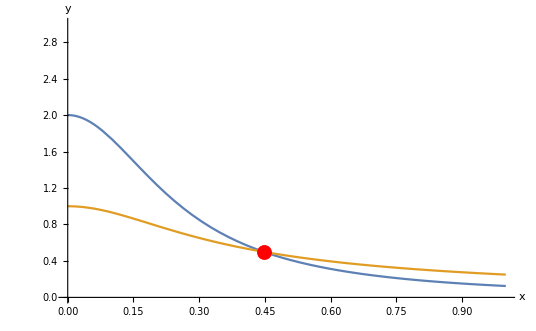

```mathematica
Plot[{f[x],g[x]},{x,0,1},AxesLabel->{"x","y"},PlotRange-> {0,3}, Epilog->{Red, PointSize[0.02], Point[{1/(√5), 1/2}]}]
```

Här har vi även lagt till en punkt som visar skärningspunkten som användas för att kunna räkna ut den efterlängtade integralen.

```mathematica
x/.Solve[f[x]==g[x],x]
```

{-1/(√5),1/(√5)}

```mathematica
Subscript[y, 1]==2/(1+15((1/(√5))^2))
Subscript[y, 2]==1/((1+15(1/(√5))^2)^(1/2))
```

y_1==1/2

y_2==1/2

För båda skärningspunkternas x-värden är y1 = y2 = 1/2.
Svar: (x_1,y_1)==(1/(√5),1/2)

Med denna skärningspunkt kan man räkna ut önskad integral till funktionerna, och genom anvädningen av formeln för att räkna ut en integral A=∫_a^b f(x)dx kunde vi lösa uppgiften på följande sätt:

```mathematica
A==NIntegrate[(f[x]),{x,0,1/(√5)}]-NIntegrate[(g[x]),{x,0,1/(√5)}]
```

A==0.200733

NIntegrate räknar ut integralen och får fram ett godtyckligt tal som resultat. Genom att ta skillnaden mellan två integraler (areror) får vi resultatet att arean är lika med 0,200733 areaenheter.

### 2.3 Uppgift 3.3)

Först rensar vi alla globala variablar från dess värden, sedan deklarerar vi varje varialbel med sitt egna värde eller formel för att de ska vara giltiga i funktionerna y_1 och y_2. Vi och deklarerar y_1 och y_2 till sina egna funktioner så att vi kan plotta dem i intervallet 0 till 5T. Vi använde oss också av PlotLegends som identifierar linjerna i grafen nedan.

```mathematica
ClearAll["Global`*"]
```

```mathematica
Subscript[A, 1] :=1
```

```mathematica
Subscript[A, 2] :=2
```

```mathematica
υ :=50
```

```mathematica
ω:=2Pi*υ
```

```mathematica
T :=1/υ
```

```mathematica
Subscript[ϕ, 1] := Pi/3
```

```mathematica
Subscript[ϕ, 2] := Pi/6
```

```mathematica
Subscript[Y, 1][t_]:=A1*Sin [ω*t+Subscript[ϕ, 1]]
```

```mathematica
Subscript[Y, 2][t_]:=A2*Sin[ω*t+Subscript[ϕ, 2]]
```

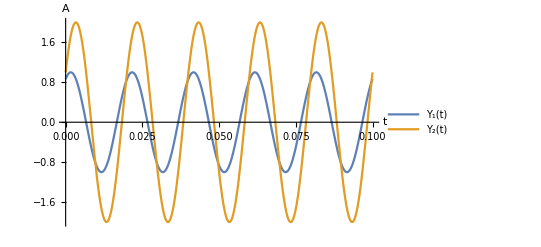

```mathematica
Plot[{Subscript[Y, 1][t],Subscript[Y, 2][t]},{t,0,5T}, PlotLegends->"Expressions", AxesLabel->{"t","A"}]
```

I grafen ovan kan man se hur funktionerna sträcker sig olika beroende på deras olika variablar.

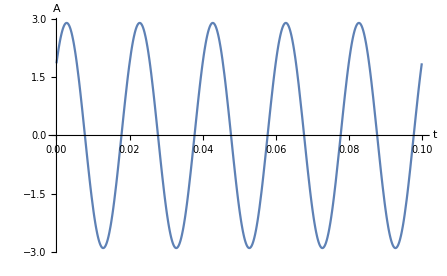

```mathematica
Plot[(Subscript[Y, 1][t]+Subscript[Y, 2][t]),{t,0,5T},AxesLabel->{"t","A"}]
```

I den andra deluppgiften ska man plotta summan av de två funktionerna  i intevallet 0 till 5T. Ovan ser man hur summan har förändrats om man jämför det med grafen som visade y_1 och y_2 som separata linjer.

```mathematica
Subscript[υ, 2] :=60
```

```mathematica
Subscript[ω, 2]:=2Pi*Subscript[υ, 2]
```

```mathematica
Subscript[Y, 3][t_] := Subscript[A, 1]*Sin [Subscript[ω, 2]*t+Subscript[ϕ, 1]]
```

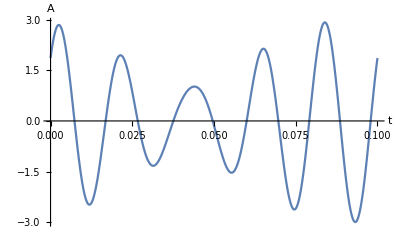

```mathematica
Plot[(Subscript[Y, 2][t]+Subscript[Y, 3][t]),{t,0,5T},AxesLabel->{"t","A"}]
```

I den sista deluppgiften plotta vi summan av y_2 och y_3, där y_3 är den modifierade versionen av funktionen y_1. Eftersom vi ändrade frekvenen υ till 60 Hz på funktionen y_1 ändrades också vinkelfrekvensen ω till 2 Pi/60.

## 3. Resultat, diskussion och slutsats

### Uppgift 3.1

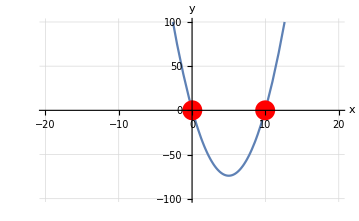
För den första uppgiften har vi fått flera resultat beroende på varje deluppgift. 

Denna tabell är en sammanställning av funktionerna, nollställen för funktionerna samt maximumvärdet av tredjegradsfunktionen som användes genom hela uppgiften. 

Ekvation | Nollställe 1 | Nollställe 2 | Nollställe 3 | Maximumvärde
f(x) = x^3-15 x^2+x+1 | 5+(2 (549+ⅈ √2517))^(1/3)/3^(2/3)+(37 2^(2/3))/(3 (549+ⅈ √2517))^(1/3) | 5-((1+ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1-ⅈ √3))/(6 (549+ⅈ √2517))^(1/3) | 5-((1-ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1+ⅈ √3))/(6 (549+ⅈ √2517))^(1/3) | y=0.0334452
f'(x) | 1/3 (15-√222) | 1/3 (15+√222) | - | -

Genom att ha använt oss av datatypen Solve har vi kunnat lösa ut nollställena för den tredjegradsfunktion, samt dess derivata, uppgiften var baserad på. I vidare steg användes dessa tal för att skapa ett intervall för att sedan med intervallet kunna få fram maximumvärdet av funktionen. I sista delen av uppgiften använde inte vi oss utav Solve. Den datatypen som användes för att hitta maximumvärdet är FindMaximum. Genom att använda sig av denna datatyp kan man på ett lätt och smidigt sätt hitta maximumvärdet för funktionen.

Graferna nedanför visar en del av resultaten, t.ex. placerar ut alla nollställen för varje funktion.

-Graphics--Graphics--Graphics-
 Tredjegradsfunktionen  f(x)=x^3-15 x^2+x+1		    Inzoomad på två av tredjegradsfunktionens nollställen	 	Andragrandsekvationen med dess nollställen
	med dess nollställen utplacerade

Tredjeradsekvationen inom intervallet [x_1,x_3]

### Uppgift 3.2

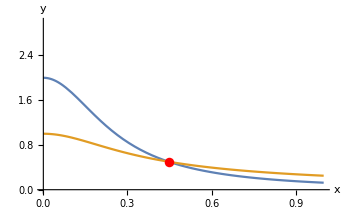
Grafen nedanför visar funktionerna samt punkten där funktionerna skär i varandra. Funktionerna som användes i uppgiften finns i tabellen som är placerad under grafen.

-Graphics-
 Funktion | Skärningspunkt för x | Skärningspunkt för y
2/(1+15 x^2)  | -1/(√5),1/(√5) | 1/2
1/(√(1+15 x^2)) | -1/(√5),1/(√5) | 1/2

För att räkna ut skärningspunkten skrev vi följande:

```mathematica
x/.Solve[f[x]==g[x],x]
```

{-1/(√5),1/(√5)}

```mathematica
Subscript[y, 1]==2/(1+15((1/(√5))^2))
Subscript[y, 2]==1/((1+15(1/(√5))^2)^(1/2))
```

y_1==1/2

```mathematica
Subscript[y, 2]==1/2
```

Skärningspunktens x-värden för dessa funktioner är lika med -1/(√5),1/(√5)då y-värdet är lika med 1/2.
Arean mellan de två funktionerna inom intervallet 0 < x < 1/(√5) räknades ut genom den formeln för skillnader av areor inom integralberäkningar: A=∫_a^b f(x)dx-∫_a^b g(x)dx; vilket leder till följande:

```mathematica
A==NIntegrate[(f[x]),{x,0,1/(√5)}]-NIntegrate[(g[x]),{x,0,1/(√5)}]
```

A==0.200733

där arean av beräknad integral är ungefär lika med 0,200733 areaenheter.

### Uppgift 3.3

Första deluppgiften:

```mathematica
Subscript[Y, 1][t_]:=A1*Sin [ω*t+Subscript[ϕ, 1]]
```

```mathematica
Subscript[Y, 2][t_]:=A2*Sin[ω*t+Subscript[ϕ, 2]]
```

-Graphics-

I grafen ser man att både funktionerna y_1 och y_2 har fem maximalavärden i intervallet [0, 5T]. 
Eftersom de två elgeneratorer har sinus formad spänning så kom vi fram till att faserna  ϕ_1ochϕ_2 har enheten Radian.

Andra deluppgiften:

```mathematica
Subscript[Y, 1][t]+Subscript[Y, 3][t]
```

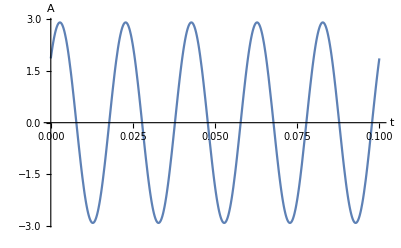

Här ser vi att y_1 och y_2 har adderat till summan som visas ovan i grafen och det vi märker är att amplituden har också adderas. I detta fall förstår vi att om man seriekopplar två elgeneratorer så förstärks amplituden mellan elgeneratorerna.

Tredje deluppgiften:

```mathematica
Subscript[Y, 2][t]+Subscript[Y, 3][t]
```

I grafen ser vi att vågens maximalavärden inte är jämlika då summan av den ena funktionens frekvens v=50 inte är likadan som den andra funktionens frekvens v=60.
När två elgeneratorer seriekopplas med olika frekvens så sker en ojämn balans i strömfördelningen och det är ingen bra sak.

### Liten slutsats

Vad har vi lärt oss? Jo, vi har lärt oss att modellera och rita ut en eller fler funktioner inom ett lämpligt intervall med hjälp av Mathematica. Vi har även lärt oss att hitta nollställen till en funktion samt lägga ut punkter som visar var dessa befinner sig i ett koordinatsystem. Tillämpning av intervall har även gjorts i detta projekt, då vi har fått lite mer erfarenhet om integralfunktioner; t.ex. att räkna ut arean mellan två funktioner. Sist men inte minst har vi även lärt oss en del hur sinusfunktioner fungerar; hur amplituder, frekvens och faser kan ha för påverkan när dessa adderas ihop. I samma övning fick vi reda på hur två elgeneratorer påverkar varandra när de seriekopplas med olika frekvenser.